```mathematica
<<Braindrop`
```

### Input Code Folding

The following code is a script that adds a button to turn all input cells off, thereby just showing the plots, outputs, and/or manipulators.

```mathematica
ShowInputCells[sh_]:=SetOptions[#,CellOpen->sh]&/@Cells[EvaluationNotebook[],CellStyle->{"Input"}]
```

```mathematica
SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[DynamicModuleBox[{showHide$$=True},TemplateBox[{"\"Show/hide input cells \"",CheckboxBox[Dynamic[showHide$$,{(showHide$$=#)&,ShowInputCells[showHide$$]&}]]},"RowDefault"],DynamicModuleValues:>{}]],"Output"]]
```

### DAC Mismatch

Let the transistor threshold difference, normalized by U_T, be Normal[0, σ].  
Let the current through branch B_i be I_i. The termination branch has current I_T
Let I_0 be our reference LSB current. Since we are dealing with ratios of currents with respect to I_0, we don’t need to include a mismatch term for I_0. That is, we always consider the LSB bit 0’s current, I_0, to be correct.

Between the bit 0 and tail, we have the current through both as

I_(0:T)= I_0(1+α_T)

The current for bit 1 is then

I_1= α_1 I_(0:T)

and the total current through bits 1 and 0 is

I_(1:0) = α_1 I_(0:T) + I_0

Extending this, for any bit i≥1, we have

I_i= α_i I_(i-1:T)
I_(i:0)= α_i I_(i-1:T)+I_(i-1:0)

```mathematica
branchCurrent[i_]:= Subscript[α, i] sumCurrent[i-1]/.Subscript[α, 0]-> 1/Subscript[α, T]
sumCurrent[j_]:= Simplify[If[j≥  0,(1+Subscript[α, j])sumCurrent[j-1],Subscript[I, 0] Subscript[α, T]]/.Subscript[α, 0]-> 1/Subscript[α, T]]
deltaBit[i_]:=Simplify[(branchCurrent[i]-(sumCurrent[i-1]- Subscript[α, T] Subscript[I, 0]))/Subscript[I, 0]-1]
```

The % difference (in terms of I_0) between any MSB i and all its LSBs (i.e., DNL) is then

Δ_i=(I_i-I_(i-1:0))/I_0-1

For example, the DNL for 4 bits has the expression

```mathematica
FullSimplify[deltaBit[3]]== 
ExpandAll[deltaBit[3]]
```

-1+(1-2 (1+α_1) (1+α_2)+2 (1+α_1) (1+α_2) α_3) α_T==-1-α_T-2 α_1 α_T-2 α_2 α_T-2 α_1 α_2 α_T+2 α_3 α_T+2 α_1 α_3 α_T+2 α_2 α_3 α_T+2 α_1 α_2 α_3 α_T

Give below are I_i, I_(i;T) and Δ_i when there is no mismatch.

```mathematica
Grid[Flatten[Append[{{{Subscript[I, i], Subscript[I, i:T], Subscript[Δ, i]}}},{branchCurrent[#],sumCurrent[#],deltaBit[#]}/.Subscript[α, _]-> 1&/@Range[0, 9]],1], Dividers-> {None, 2-> True}]
```

I_i | I_(i:T) | Δ_i
I_0 | 2 I_0 | 0
2 I_0 | 4 I_0 | 0
4 I_0 | 8 I_0 | 0
8 I_0 | 16 I_0 | 0
16 I_0 | 32 I_0 | 0
32 I_0 | 64 I_0 | 0
64 I_0 | 128 I_0 | 0
128 I_0 | 256 I_0 | 0
256 I_0 | 512 I_0 | 0
512 I_0 | 1024 I_0 | 0

and with mismatch, for a few bits

```mathematica
Grid[Insert[{#, branchCurrent[#], sumCurrent[#], deltaBit[#]}&/@Range[0, 3],{b,Subscript[I, i], Subscript[I, i:T], Subscript[Δ, i]},1], Dividers-> {None, 2-> True}]
```

b | I_i | I_(i:T) | Δ_i
0 | I_0 | I_0 (1+α_T) | 0
1 | I_0 α_1 (1+α_T) | I_0 (1+α_1) (1+α_T) | -2+α_1 (1+α_T)
2 | I_0 (1+α_1) α_2 (1+α_T) | I_0 (1+α_1) (1+α_2) (1+α_T) | -2+α_1 (-1+α_2) (1+α_T)+α_2 (1+α_T)
3 | I_0 (1+α_1) (1+α_2) α_3 (1+α_T) | I_0 (1+α_1) (1+α_2) (1+α_3) (1+α_T) | -1+α_T-(1+α_1) (1+α_2) (1+α_T)+(1+α_1) (1+α_2) α_3 (1+α_T)

### Analytical expression for R-2R variance

```mathematica
σLogNormal[σn_]=StandardDeviation[LogNormalDistribution[0, σn]];
σNormal[σl_]=σn/.FullSimplify[Solve[StandardDeviation[LogNormalDistribution[0, σn]]== σl, σn][[4]], σn>0&&σl>0][[1]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
R2RStd[b_, σn_]:= StandardDeviation[TransformedDistribution[Evaluate[deltaBit[b]/.Subscript[α, T]-> Subscript[α, 0]], (Subscript[α, #]\[Distributed]LogNormalDistribution[0, σn])&/@Range[0, b]]]
```

For 2 bits, the variance in terms of the underlying Normal’s variance σn  is:

```mathematica
FullSimplify[R2RStd[1, σn], σn>0]
```

√(ⅇ^(σn^2) (-1+ⅇ^(σn^2/2) (-2+2 ⅇ^(σn^2)+ⅇ^((5 σn^2)/2))))

In terms of the variance of the LogNormal σl, this becomes

```mathematica
FullSimplify[R2RStd[1, σNormal[σl]], σl>0]
```

σl √(2+σl^2+√(1+4 σl^2)+√2 √(1+√(1+4 σl^2)))

The resultant ditribution of the mismatch between MSB and its LSBs is more Normal than LogNormal as seen below for 6 bits.

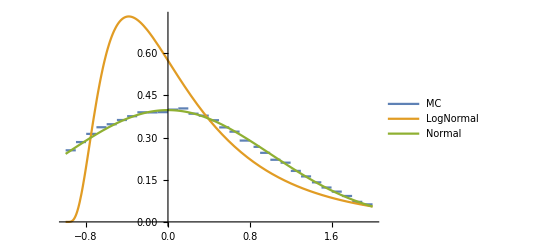

```mathematica
With[{b=5, σn=0.125/4},distR2R = TransformedDistribution[deltaBit[b]/.Subscript[α, T]-> Subscript[α, 0], (Subscript[α, #]\[Distributed]LogNormalDistribution[0, σn])&/@Range[0, b]];
distData = RandomVariate[distR2R, 100000];
distHist = HistogramDistribution[distData, 100];
σR2R = R2RStd[b,σn];
p1 = PDF[distHist, x];
p2 = PDF[LogNormalDistribution[0, σNormal[σR2R]]][x+1];
p3 = PDF[NormalDistribution[0, σR2R]][x];
Plot[{p1, p2, p3}, {x, -1, 2}, PlotLegends->{"MC", "LogNormal", "Normal"}, PlotRange->All]]
```

### Simulation

The distribution of Δ_i for σ=0.125/4, for different bit widths are given below

```mathematica
SeedRandom[1234];
deltaMC=With[{σ= 0.125/4, numSamples=100000},Table[deltaBit[b]/.Flatten[{{Subscript[α, T]-> RandomVariate[LogNormalDistribution[0, σ],numSamples]},(Subscript[α, #]-> RandomVariate[LogNormalDistribution[0, σ],numSamples]&/@Range[1,b])}, 1],{b,1,9}]];
```

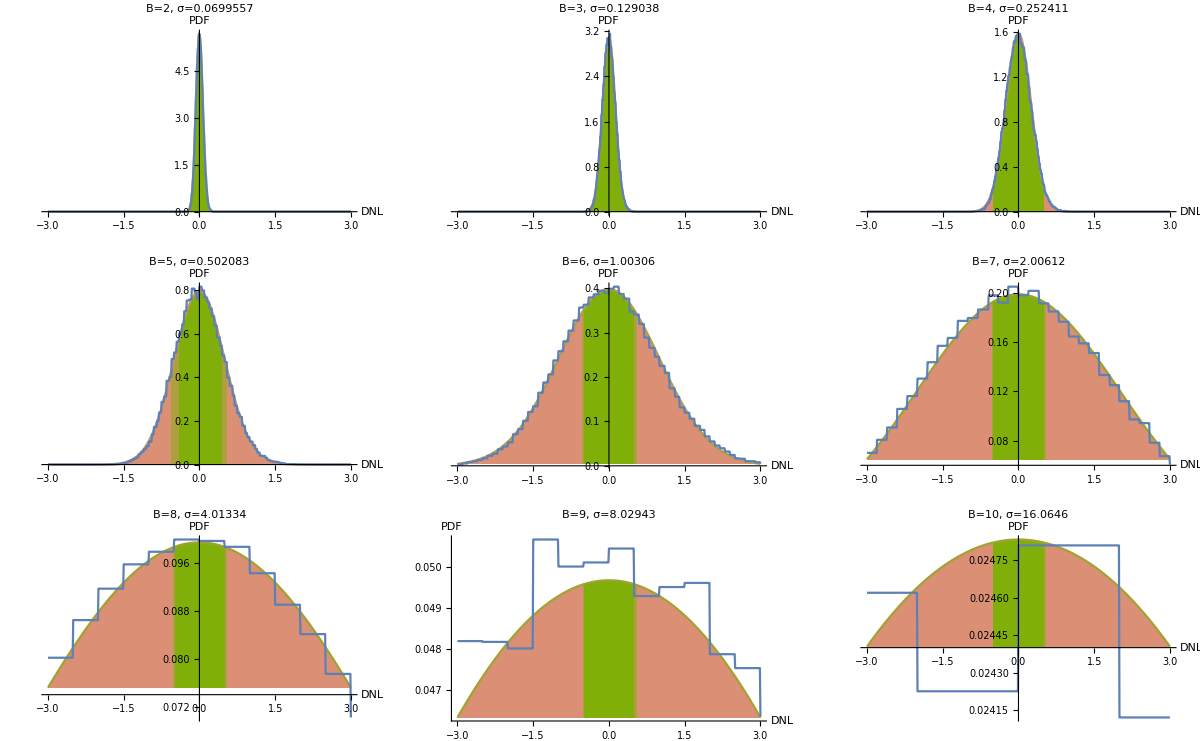

```mathematica
distPlots = Reap[
(errHistDist = HistogramDistribution[deltaMC[[#]], 100];
errDistFit = NormalDistribution[0, R2RStd[#,0.125/4]];
p1 =Plot[PDF[errDistFit, x], {x, -3, 3},PlotRange->All, AxesLabel->{"DNL", "PDF"}, Filling-> Bottom,ColorFunction->(If[-0.5≤#1≤0.5,ColorData[8,"ColorList"][[6]],ColorData[8,"ColorList"][[3]]]&),ColorFunctionScaling->False, PlotLabel-> "B="<>IntegerString[#+1]<>", σ=" <> ToString[ StandardDeviation[errDistFit]]];
p2 = DiscretePlot[PDF[errHistDist, x], {x, -3, 3, 0.01},PlotRange->All, Filling->None, Joined-> True];
Sow[Show[{p1, p2}]])&/@Range[1, 9]];
GraphicsGrid[ArrayReshape[distPlots[[2]], {3, 3}], ImageSize->Full]
```

The standard deviation goes roughly as
DNL[B]=2^(B-1)(ⅇ^(σ/n)-1)

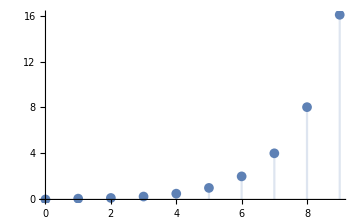

b | σ
0 | 0
1 | 0.0699557
2 | 0.129038
3 | 0.252411
4 | 0.502083
5 | 1.00306
6 | 2.00612
7 | 4.01334
8 | 8.02943
9 | 16.0646

```mathematica
Reap[DiscretePlot[Sow[R2RStd[b,0.125/4]], {b, 0, 9}, ImageSize-> Medium]];
%[[1]]
Grid[Insert[{#, %%[[2]][[1]][[# + 1]]}&/@Range[0, 9], {b, σ}, 1],Dividers-> {None, 2-> True}]
```

n, such that σ_I'→σ_I/n for 99.73% for various number of b bits are given below (b→{n, %, σ_Δ}).

```mathematica
Table[Insert[Catch[Table[SeedRandom[1234];
(* estDist = EstimatedDistribution[ deltaBit[b]/.Flatten[{{Subscript[α, T]-> RandomVariate[LogNormalDistribution[0, 0.125/n],100000]},(Subscript[α, #]-> RandomVariate[LogNormalDistribution[0, 0.125/n],100000]&/@Range[1,b])}, 1], NormalDistribution[μn, σn]]; *)

estDist = NormalDistribution[0, R2RStd[b,0.125/n]];
pres=Probability[-0.5≤ x≤ 0.5, x\[Distributed]estDist];If[pres≥ 0.9973, Throw[{n,pres, StandardDeviation[estDist]}]], {n, 1, 1000}]],b+1,1], {b, 1, 5}];
Grid[Insert[%, {B, n,Subscript[P, 0.5],σ}, 1],Dividers-> {None, 2-> True}]
```

B | n | P_0.5 | σ
2 | 2 | 0.999631 | 0.140384
3 | 4 | 0.999893 | 0.129038
4 | 7 | 0.999481 | 0.144056
5 | 13 | 0.998817 | 0.154179
6 | 25 | 0.998211 | 0.160089

### Thermometer mismatch

For thermometer code, every bit is an LSB. So the DNL is given by
(I_0(α_i+α_(i-1))-I_0 α_(i-1))/I_0-1=α_i-1

The distribution of DNL for various σ/n is plotted below.

```mathematica
errDistThermometer[σ_]:=TransformedDistribution[α-1,α\[Distributed]LogNormalDistribution[0, σ]]
```

```mathematica
plotList=Table[With[{σ=0.125/n},probValid = Probability[Abs[x]≤ 0.5, x\[Distributed]errDistThermometer[σ]];
Plot[PDF[errDistThermometer[σ], x], {x, -1, 1}, AxesLabel-> {"DNL", "PDF"}, PlotLabel-> "n^2="<>ToString[n^2]<>", P(|DNL|≤0.5)="<>ToString[probValid], PlotRange->All]], {n, 1, 2, 0.1}];
```

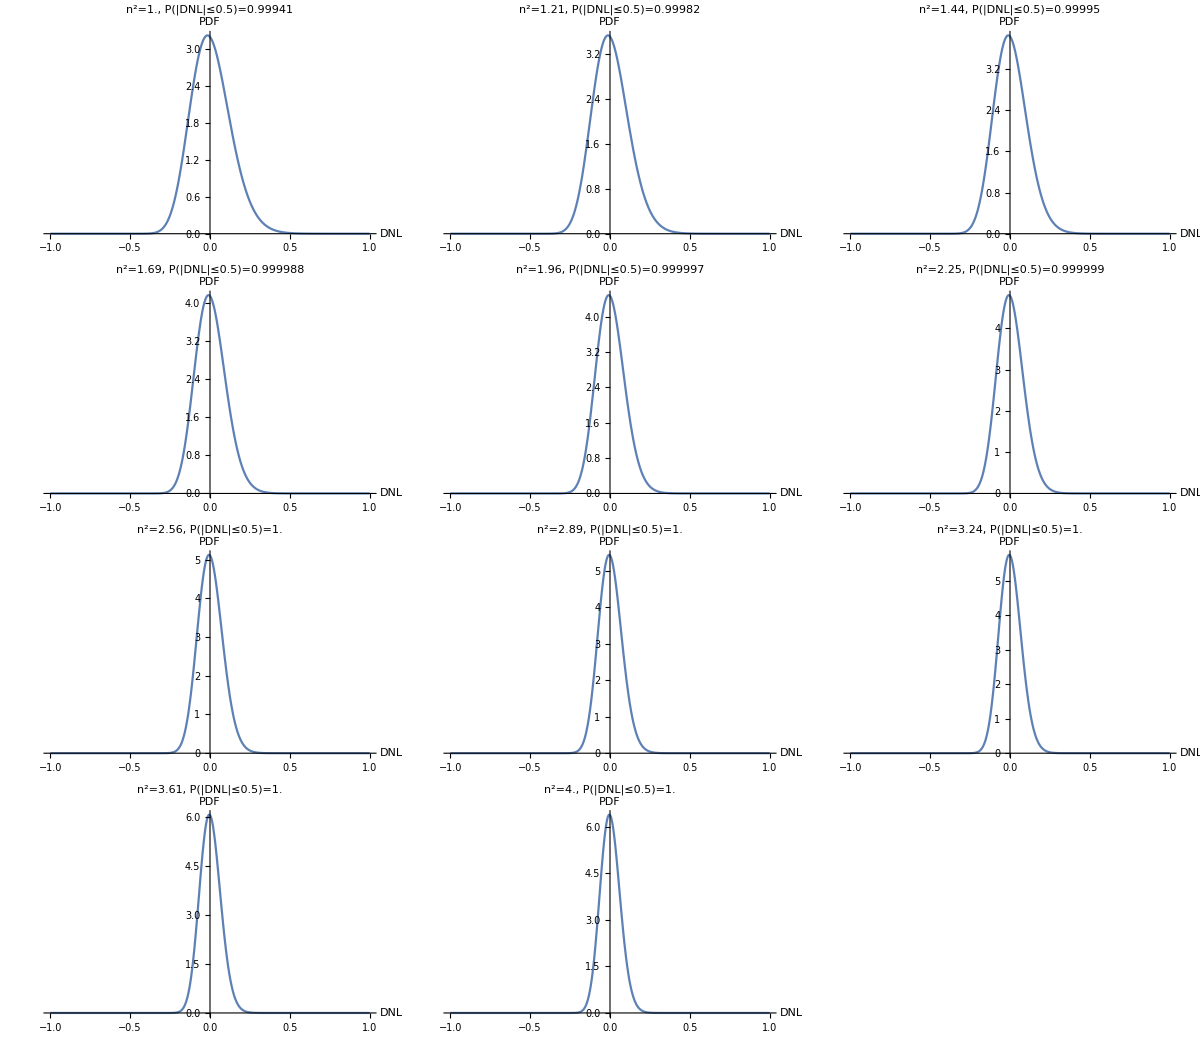

```mathematica
GraphicsGrid[ArrayReshape[plotList, {4, 3}], ImageSize->Full, Spacings-> {0, 0}]
```

So, 2048 transistors will give me better linearity than the best R-2R with way lesser number of transistors.

Note that, for a Normal random variable, 4σ has the probability

```mathematica
N[Probability[Abs[x]≤ 4 σ, x\[Distributed]NormalDistribution[0, σ]],12]
```

0.999936657516

### Segmented

The DNL is (α_M I_ref-(I_ref-α_T I_0))/I_0-1, where I_ref is the total current fed into the R-2R network.
For B bits of R-2R network, I_0 is given by I_ref/((1+α_T)(Π_(i=1))^(B-1)(1+α_i))

```mathematica
dnlSegmented[b_]:=Simplify[(Subscript[α, M] Subscript[I, ref]-(Subscript[I, ref]-Subscript[α, T] Subscript[I, 0]))/Subscript[I, 0]-1/.Subscript[I, ref]-> sumCurrent[b], Subscript[α, _]>0]
segmentedStd[b_, σ_]:= StandardDeviation[TransformedDistribution[dnlSegmented[b]/.{Subscript[α, T]-> Subscript[α, 0], Subscript[α, M]-> Subscript[α, b+1]},Subscript[α, #]\[Distributed]LogNormalDistribution[0, σ]&/@Range[0,b+1]]]
```

n, such that σ_I'→σ_I/n for 99.73% for various number of b bits for R-2R are given below.

```mathematica
Table[Insert[Catch[Table[SeedRandom[1234];
estDist = NormalDistribution[0, segmentedStd[b,0.125/n]];
pres=Probability[-0.5≤ x≤ 0.5, x\[Distributed]estDist];If[pres≥ 0.9973, Throw[{n,pres, StandardDeviation[estDist]}]], {n, 1, 1000}]],b+1,1], {b, 0, 5}];
Grid[Insert[%, {B, n,Subscript[P, 0.5],σ}, 1],Dividers-> {None, 2-> True}]
```

B | n | P_0.5 | σ
1 | 2 | 0.999631 | 0.140384
2 | 4 | 0.999893 | 0.129038
3 | 7 | 0.999481 | 0.144056
4 | 13 | 0.998817 | 0.154179
5 | 25 | 0.998211 | 0.160089
6 | 49 | 0.997802 | 0.163288

### Scratchpad

The variance of R-2R for 1 to 5 bits:

```mathematica
Grid[Table[{b->FullSimplify[R2RStd[b, σn], σn>0]}, {b, 0, 4}]]
```

0→√(ⅇ^(σn^2) (-1+ⅇ^(σn^2)))
1→√(ⅇ^(σn^2) (-1+4 ⅇ^(σn^2/2)-3 ⅇ^(σn^2)-4 ⅇ^((3 σn^2)/2)+4 ⅇ^(3 σn^2)))
2→√(ⅇ^(σn^2) (-1+ⅇ^(σn^2) (5+4 ⅇ^(σn^2) (-4+2 ⅇ^(σn^2)+ⅇ^(3 σn^2)))))
3→√(ⅇ^(σn^2) (-1-4 ⅇ^(σn^2/2)+ⅇ^(σn^2)+16 ⅇ^((3 σn^2)/2)-8 ⅇ^(2 σn^2)-36 ⅇ^((5 σn^2)/2)+8 ⅇ^(3 σn^2)+16 ⅇ^((7 σn^2)/2)-16 ⅇ^(4 σn^2)+12 ⅇ^(5 σn^2)+8 ⅇ^((11 σn^2)/2)+4 ⅇ^(7 σn^2)))
4→√(ⅇ^(σn^2) (-1-8 ⅇ^(σn^2/2)-15 ⅇ^(σn^2)+16 ⅇ^((3 σn^2)/2)+36 ⅇ^(2 σn^2)-40 ⅇ^((5 σn^2)/2)-60 ⅇ^(3 σn^2)+32 ⅇ^((7 σn^2)/2)-4 ⅇ^(4 σn^2)-64 ⅇ^((9 σn^2)/2)+24 ⅇ^(5 σn^2)+48 ⅇ^((11 σn^2)/2)+16 ⅇ^(7 σn^2)+16 ⅇ^((15 σn^2)/2)+4 ⅇ^(9 σn^2)))